# Лабораторная работа №14

Выполнила студентка ММФ БГУ
КМ, 1 к, 5 гр . Ковалевская В . С .
    8 декабря 2021

Вариант 12

x -x^2 y^2=y^2, y(1)>0

## Представление неявной функции

### Задание 7.15

```mathematica
ClearAll[F,x,y,f];
F[x_,y_]:=x -x^2 y^2-y^2;
```

```mathematica
F[3,5]
```

-247

```mathematica
F[x,y]==0
```

x-y^2-x^2 y^2==0

### 7.16

```mathematica
Plot3D[F[x,y],{x,-2,2},{y,-2,2},PlotRange->{-3,3},ClippingStyle->None]
```

-Graphics3D-

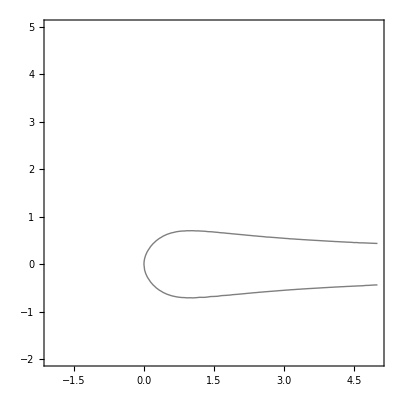

```mathematica
ContourPlot[F[x,y],{x,-2,5},{y,-2,5},PlotRange->{-7,7},Contours->{0},AspectRatio->Automatic,ImageSize->400,ContourShading->False]
```

### 7.17

```mathematica
x0=1
F[x0,y]==0
```

1

1-2 y^2==0

```mathematica
FindRoot[%,{y,.6}]
```

{y→0.707107}

```mathematica
f[x0]=y/.%(*для начального значения аргумента х0=1 вычислили приближенно значение функции*)
```

0.707107

```mathematica
?x0
```

```mathematica
?f
```

```mathematica
{x0,f[x0]}
```

{1,0.707107}

## Производная неявной функции

### 7.18

Производная функции, заданной неявно.
F[x,y]= -F'x[x,y]/F'y[x,y], т.е.
F[x,y]=-D[x -x^2 y^2-y^2,x]/D[x -x^2 y^2-y^2,y]

```mathematica
D[x -x^2 y^2-y^2,x]
```

1-2 x y^2

```mathematica
D[x -x^2 y^2-y^2,y]
```

-2 y-2 x^2 y

F[x,y]= (1-2 x y^2)/(2 y+2 x^2 y)

```mathematica
Dt[F[x,y]]
```

Dt[x]-2 x y^2 Dt[x]-2 y Dt[y]-2 x^2 y Dt[y]

```mathematica
Dt[y]/.y->f[x]
```

Dt[x] f'[x]

```mathematica
Dt[F[x,y]==0]/.y->f[x]
```

Dt[x]-2 x Dt[x] f[x]^2-2 Dt[x] f[x] f'[x]-2 x^2 Dt[x] f[x] f'[x]==0

```mathematica
f'[x]//FullForm
```

Derivative[1][f][x]

```mathematica
Dt[F[x,y]==0]/.y->f[x];
Solve[%,f'[x]]
Der1=First@%(*чему равна первая производная ассоциировали с символом Der1*)
```

{{f'[x]→(1-2 x f[x]^2)/(2 (1+x^2) f[x])}}

{f'[x]→(1-2 x f[x]^2)/(2 (1+x^2) f[x])}

```mathematica
?Der1
```

## Многочлен Тейлора неявной ф-ции

### 7.19

Der[n] – n -я производная y = f (x);
c[n] – значение n-ой производной y = f (x) в точке x0

```mathematica
ClearAll[Der,c];
c[0]=f[x0]
```

0.707107

```mathematica
Der[1]=f'[x]/.Der1
c[1]=f'[x]=%/.x->x0
```

(1-2 x f[x]^2)/(2 (1+x^2) f[x])

-7.85046×10^-17

```mathematica
f'[t]//FullForm
```

Derivative[1][f][t]

```mathematica
f''[t]//FullForm
```

Derivative[2][f][t]

```mathematica
Derivative[3][f][t]
```

f^(3)[t]

```mathematica
?Der
```

```mathematica
D[Der[1],x](*ищем вторую производную*)
```

(3.14018×10^-16 x f[x]-2 f[x]^2)/(2 (1+x^2) f[x])+(3.92523×10^-17 (1-2 x f[x]^2))/((1+x^2) f[x]^2)-(x (1-2 x f[x]^2))/((1+x^2)^2 f[x])

```mathematica
%/.Der1
```

(3.14018×10^-16 x f[x]-2 f[x]^2)/(2 (1+x^2) f[x])+(3.92523×10^-17 (1-2 x f[x]^2))/((1+x^2) f[x]^2)-(x (1-2 x f[x]^2))/((1+x^2)^2 f[x])

```mathematica
Der[2]=%//Together
```

(3.92523×10^-17+3.92523×10^-17 x^2-1. x f[x]+7.85046×10^-17 x f[x]^2+7.85046×10^-17 x^3 f[x]^2-1. f[x]^3+x^2 f[x]^3)/((1.+x^2)^2 f[x]^2)

```mathematica
c[2]=f''[x0]=%/.x->x0(*ищем значение второй производной в точке х0*)
```

-0.353553

```mathematica
Der[3]=Together[D[Der[2],x]/.Der1](*аналогично находим третью производную и ее значение в точке*)
c[3]=Derivative[3][f][x0]=%/.x->x0
```

1/((1.+x^2)^3 f[x]^3)(6.16298×10^-33+1.2326×10^-32 x^2+6.16298×10^-33 x^4-1.57009×10^-16 x f[x]-1.57009×10^-16 x^3 f[x]-1. f[x]^2+3. x^2 f[x]^2+1.57009×10^-16 f[x]^3-1.57009×10^-16 x^4 f[x]^3+6. x f[x]^4-2. x^3 f[x]^4)

0.707107

```mathematica
Ν=20;
Do[Der[n]=Together[D[Der[n-1],x]/.Der1];
c[n]=Derivative[n][f][x0]=Der[n]/.x->x0,{n,4,Ν}];
```

```mathematica
Do[Print["Der[",n,"]=",Der[n]=Together[D[Der[n-1],x]/.Der1]];
Print["c[",n,"]=",c[n]=Derivative[n][f][x0]=Der[n]/.x->x0],{n,4,7}];
```

Der[4]=1/((1.+x^2)^4 f[x]^4)(1.45147×10^-48+4.3544×10^-48 x^2+4.3544×10^-48 x^4+1.45147×10^-48 x^6-3.69779×10^-32 x f[x]-7.39557×10^-32 x^3 f[x]-3.69779×10^-32 x^5 f[x]-2.35514×10^-16 f[x]^2+4.71028×10^-16 x^2 f[x]^2+7.06542×10^-16 x^4 f[x]^2+12. x f[x]^3-12. x^3 f[x]^3-1.41308×10^-15 x f[x]^4-9.42055×10^-16 x^3 f[x]^4+4.71028×10^-16 x^5 f[x]^4+6. f[x]^5-36. x^2 f[x]^5+6. x^4 f[x]^5)

c[4]=-1.06066

Der[5]=1/((1.+x^2)^5 f[x]^5)(4.55787×10^-64+1.82315×10^-63 x^2+2.73472×10^-63 x^4+1.82315×10^-63 x^6+4.55787×10^-64 x^8-1.16117×10^-47 x f[x]-3.48352×10^-47 x^3 f[x]-3.48352×10^-47 x^5 f[x]-1.16117×10^-47 x^7 f[x]-7.39557×10^-32 f[x]^2+7.39557×10^-32 x^2 f[x]^2+3.69779×10^-31 x^4 f[x]^2+2.21867×10^-31 x^6 f[x]^2+3.76822×10^-15 x f[x]^3-3.76822×10^-15 x^5 f[x]^3+12. f[x]^4-120. x^2 f[x]^4+60. x^4 f[x]^4-1.88411×10^-15 f[x]^5+9.42055×10^-15 x^2 f[x]^5+9.42055×10^-15 x^4 f[x]^5-1.88411×10^-15 x^6 f[x]^5-120. x f[x]^6+240. x^3 f[x]^6-24. x^5 f[x]^6)

c[5]=6.28037×10^-16

Der[6]=1/((1.+x^2)^6 f[x]^6)(1.78907×10^-79+8.94535×10^-79 x^2+1.78907×10^-78 x^4+1.78907×10^-78 x^6+8.94535×10^-79 x^8+1.78907×10^-79 x^10-4.55787×10^-63 x f[x]-1.82315×10^-62 x^3 f[x]-2.73472×10^-62 x^5 f[x]-1.82315×10^-62 x^7 f[x]-4.55787×10^-63 x^9 f[x]-2.90293×10^-47 f[x]^2+1.74176×10^-46 x^4 f[x]^2+2.32235×10^-46 x^6 f[x]^2+8.7088×10^-47 x^8 f[x]^2+1.47911×10^-30 x f[x]^3+1.47911×10^-30 x^3 f[x]^3-1.47911×10^-30 x^5 f[x]^3-1.47911×10^-30 x^7 f[x]^3+4.71028×10^-15 f[x]^4-4.23925×10^-14 x^2 f[x]^4-2.35514×10^-14 x^4 f[x]^4+2.35514×10^-14 x^6 f[x]^4-8.75812×10^-47 f[x]^5-360. x f[x]^5-8.75812×10^-47 x^2 f[x]^5+1200. x^3 f[x]^5-360. x^5 f[x]^5-8.75812×10^-47 x^6 f[x]^5-8.75812×10^-47 x^8 f[x]^5+4.71028×10^-14 x f[x]^6-4.71028×10^-14 x^3 f[x]^6-8.4785×10^-14 x^5 f[x]^6+9.42055×10^-15 x^7 f[x]^6-120. f[x]^7+1800. x^2 f[x]^7-1800. x^4 f[x]^7+120. x^6 f[x]^7)

c[6]=10.6066

Der[7]=1/((1.+x^2)^7 f[x]^7)(8.42702×10^-95+5.05621×10^-94 x^2+1.26405×10^-93 x^4+1.6854×10^-93 x^6+1.26405×10^-93 x^8+5.05621×10^-94 x^10+8.42702×10^-95 x^12-2.14688×10^-78 x f[x]-1.07344×10^-77 x^3 f[x]-2.14688×10^-77 x^5 f[x]-2.14688×10^-77 x^7 f[x]-1.07344×10^-77 x^9 f[x]-2.14688×10^-78 x^11 f[x]-1.36736×10^-62 f[x]^2-1.36736×10^-62 x^2 f[x]^2+8.20417×10^-62 x^4 f[x]^2+1.91431×10^-61 x^6 f[x]^2+1.5041×10^-61 x^8 f[x]^2+4.10209×10^-62 x^10 f[x]^2+6.96704×10^-46 x f[x]^3+1.39341×10^-45 x^3 f[x]^3-1.39341×10^-45 x^7 f[x]^3-6.96704×10^-46 x^9 f[x]^3+2.21867×10^-30 f[x]^4-1.77494×10^-29 x^2 f[x]^4-3.10614×10^-29 x^4 f[x]^4+1.10934×10^-29 x^8 f[x]^4-6.87553×10^-63 f[x]^5-1.6957×10^-13 x f[x]^5-1.37511×10^-62 x^2 f[x]^5+3.95663×10^-13 x^3 f[x]^5-6.87553×10^-63 x^4 f[x]^5+3.95663×10^-13 x^5 f[x]^5-6.87553×10^-63 x^6 f[x]^5-1.6957×10^-13 x^7 f[x]^5-1.37511×10^-62 x^8 f[x]^5-6.87553×10^-63 x^10 f[x]^5-360. f[x]^6-1.75162×10^-45 x f[x]^6+7560. x^2 f[x]^6-1.75162×10^-45 x^3 f[x]^6-12600. x^4 f[x]^6+2520. x^6 f[x]^6+1.05097×10^-45 x^7 f[x]^6+1.05097×10^-45 x^9 f[x]^6+5.65233×10^-14 f[x]^7-7.91327×10^-13 x^2 f[x]^7+2.01948×10^-28 x^4 f[x]^7+7.91327×10^-13 x^6 f[x]^7-5.65233×10^-14 x^8 f[x]^7+5040. x f[x]^8-25200. x^3 f[x]^8+15120. x^5 f[x]^8-720. x^7 f[x]^8)

c[7]=-63.6396

```mathematica
Taylor[x_]=∑_(n=0)^Ν c[n]/(n!) (x-x0)^n
```

0.707107-7.85046×10^-17 (-1+x)-0.176777 (-1+x)^2+0.117851 (-1+x)^3-0.0441942 (-1+x)^4+5.23364×10^-18 (-1+x)^5+0.0147314 (-1+x)^6-0.0126269 (-1+x)^7+0.00552427 (-1+x)^8+1.46547×10^-18 (-1+x)^9-0.00220971 (-1+x)^10+0.00200883 (-1+x)^11-0.000920712 (-1+x)^12+1.67722×10^-19 (-1+x)^13+0.000394591 (-1+x)^14-0.000368285 (-1+x)^15+0.000172633 (-1+x)^16+1.09076×10^-19 (-1+x)^17-0.000076726 (-1+x)^18+0.0000726878 (-1+x)^19-0.0000345267 (-1+x)^20

### 7.20

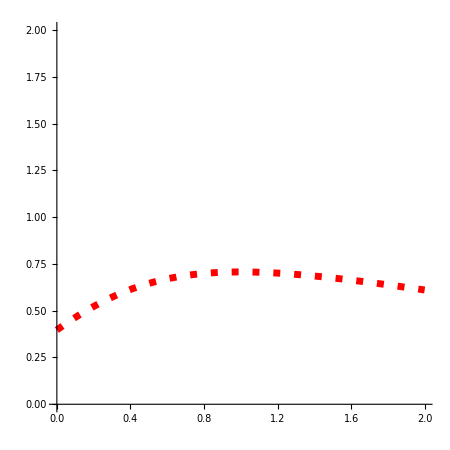

```mathematica
Plot[Taylor[x],{x,0,2},PlotRange->{0,2},AspectRatio->Automatic,ImageSize->450,PlotStyle->{AbsoluteThickness[5],AbsoluteDashing[{5,10}],Hue[3]}]
```

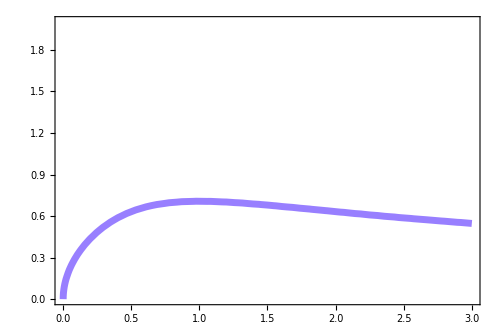

```mathematica
Fig["Contour"]=
Graphics[ContourPlot[F[x,y],{x,0,3},{y,0,2},PlotRange->{-2,2},Contours->{0},AspectRatio->Automatic,ContourShading->False,ContourStyle->{Thickness[.01],Hue[.7]},ImageSize->500]]
```

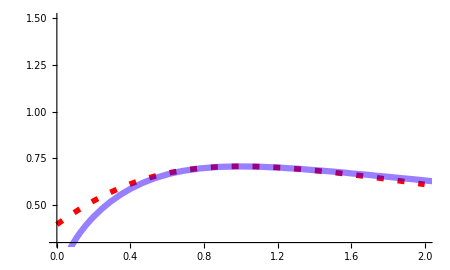

```mathematica
Show[Plot[Taylor[x],{x,0,2},PlotRange->{0.3,1.5},AspectRatio->Automatic,ImageSize->450,PlotStyle->{AbsoluteThickness[4],AbsoluteDashing[{5,10}],Hue[0]}],Fig["Contour"]]
```

## Аппроксимация Паде неявной функции

### 7.21

```mathematica
ClearAll[Pade,Num,Den,a,b];
Μ=Ν/2;
Format[a[n_Integer]]:=Subscript[a, n];
Format[b[n_Integer]]:=Subscript[b, n];
```

```mathematica
Pade[x_]=(Num[x_]=∑_(n=0)^Μ a[n] (x-x0)^n)/(Den[x_]=1+∑_(n=1)^Μ b[n] (x-x0)^n)
```

(a_0+(-1+x) a_1+(-1+x)^2 a_2+(-1+x)^3 a_3+(-1+x)^4 a_4+(-1+x)^5 a_5+(-1+x)^6 a_6+(-1+x)^7 a_7+(-1+x)^8 a_8+(-1+x)^9 a_9+(-1+x)^10 a_10)/(1+(-1+x) b_1+(-1+x)^2 b_2+(-1+x)^3 b_3+(-1+x)^4 b_4+(-1+x)^5 b_5+(-1+x)^6 b_6+(-1+x)^7 b_7+(-1+x)^8 b_8+(-1+x)^9 b_9+(-1+x)^10 b_10)

```mathematica
vars=Join[Array[a,Μ+1,0],Array[b,Μ]]
```

{a_0,a_1,a_2,a_3,a_4,a_5,a_6,a_7,a_8,a_9,a_10,b_1,b_2,b_3,b_4,b_5,b_6,b_7,b_8,b_9,b_10}

```mathematica
Num[x]-Den[x] Taylor[x];
```

```mathematica
Collect[Num[x]-Den[x] Taylor[x],x];
```

```mathematica
CoefficientList[Collect[Num[x]-Den[x] Taylor[x],x],x];
```

```mathematica
Take[CoefficientList[Collect[Num[x]-Den[x] Taylor[x],x],x],Ν+1];
```

```mathematica
Thread[Take[CoefficientList[Collect[Num[x]-Den[x] Taylor[x],x],x],Ν+1]==0];
```

```mathematica
Solve[Thread[Take[CoefficientList[Collect[Num[x]-Den[x] Taylor[x],x],x],Ν+1]==0],vars]
```

{{a_0→0.707107,a_1→2.90723,a_2→5.53884,a_3→6.41637,a_4→4.95605,a_5→2.61599,a_6→0.917895,a_7→0.188922,a_8→0.0103706,a_9→-0.00480749,a_10→-0.000984134,b_1→4.11145,b_2→8.08313,b_3→9.93542,b_4→8.40728,b_5→5.09389,b_6→2.22942,b_7→0.693701,b_8→0.146451,b_9→0.018895,b_10→0.00112879}}

```mathematica
Apply[Set,First[Solve[Thread[Take[CoefficientList[Collect[Num[x]-Den[x] Taylor[x],x],x],Ν+1]==0],vars]],1];
Pade[x]
```

(0.707107+2.90723 (-1+x)+5.53884 (-1+x)^2+6.41637 (-1+x)^3+4.95605 (-1+x)^4+2.61599 (-1+x)^5+0.917895 (-1+x)^6+0.188922 (-1+x)^7+0.0103706 (-1+x)^8-0.00480749 (-1+x)^9-0.000984134 (-1+x)^10)/(1+4.11145 (-1+x)+8.08313 (-1+x)^2+9.93542 (-1+x)^3+8.40728 (-1+x)^4+5.09389 (-1+x)^5+2.22942 (-1+x)^6+0.693701 (-1+x)^7+0.146451 (-1+x)^8+0.018895 (-1+x)^9+0.00112879 (-1+x)^10)

### 7.22

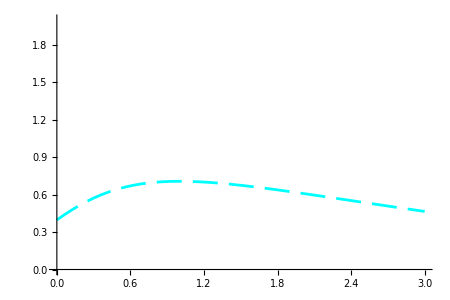

```mathematica
Plot[{Pade[x]},{x,0,3},PlotRange->{0,2},AspectRatio->Automatic,ImageSize->450,PlotStyle->{{AbsoluteThickness[2],AbsoluteDashing[{18,8}],Hue[.5]},{AbsoluteThickness[4],AbsoluteDashing[{5,10}],Hue[0]}}]
```

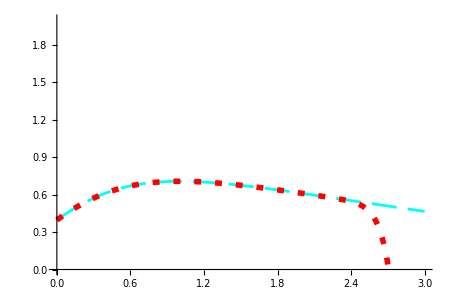

```mathematica
Plot[{Pade[x],Taylor[x]},{x,0,3},PlotRange->{0,2},AspectRatio->Automatic,ImageSize->450,PlotStyle->{{AbsoluteThickness[2],AbsoluteDashing[{18,8}],Hue[.5]},{AbsoluteThickness[4],AbsoluteDashing[{5,10}],Hue[0]}}]
```

```mathematica
Fig["Contour"]
```

-Graphics-

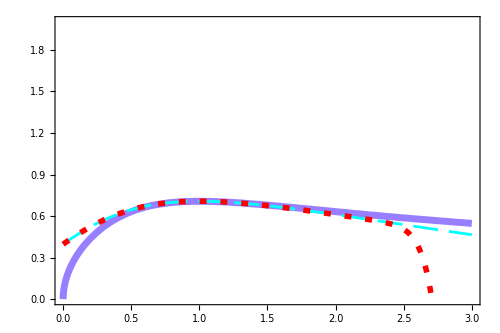

```mathematica
Show[Fig["Contour"],Plot[{Pade[x],Taylor[x]},{x,0,3},PlotRange->{0,2},AspectRatio->Automatic,ImageSize->450,PlotStyle->{{AbsoluteThickness[2],AbsoluteDashing[{18,8}],Hue[.5]},{AbsoluteThickness[4],AbsoluteDashing[{5,10}],Hue[0]}}]]
```